```mathematica
data1={{0,11.26},{100,11.26},{200,11.26},{300,11.25},{400,11.24},{500,11.22},{600,11.21},{700,11.19},{800,11.16},{900,11.14},{1000,11.11},{1100,11.07},{1200,11.04},{1221.5,11.03}};
```

```mathematica
nlm1=NonlinearModelFit[data1, a^2 -b^2 x^2,{a,b},x]
```

FittedModel[11.2633-1.55946×10^-7 x^2]

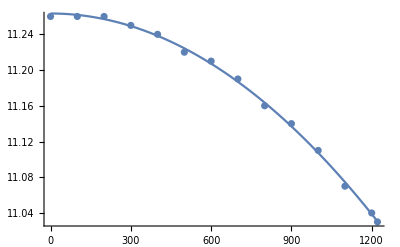

```mathematica
Show[ListPlot[data1],Plot[nlm1[x],{x,0,1221.5}]]
```

```mathematica
data2 = {{1300,10.31},{1400,10.25},{1500,10.19},{1600,10.12},{1700,10.05},{1800,9.99},{1900,9.91},{2000,9.84},{2100,9.75},{2200,9.67},{2300,9.58},{2400,9.48},{2500,9.38},{2600,9.28},{2700,9.17},{2800,9.05},{2900,8.93},{3000,8.80},{3100,8.66},{3200,8.51},{3300,8.36},{3400,8.20},{3480,8.06}};
```

```mathematica
nlm2=NonlinearModelFit[data2, a^2 -b^2 x^2,{a,b},x]
```

FittedModel[10.6835-2.11853×10^-7 x^2]

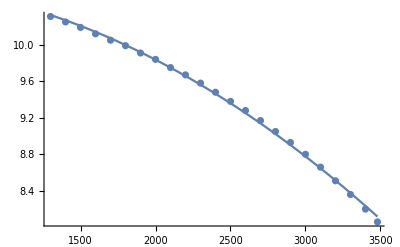

```mathematica
Show[ListPlot[data2],Plot[nlm2[x],{x,1300,3480}]]
```

```mathematica
data3={{3480,13.72},{3500,13.69},{3600,13.68},{3700,13.60},{3800,13.48},{3900,13.36},{4000,13.25},{4100,13.13},{4200,13.02},{4300,12.90},{4400,12.78},{4500,12.67},{4600,12.54},{4700,12.42},{4800,12.29},{4900,12.16},{5000,12.02},{5100,11.88},{5200,11.78},{5300,11.58},{5400,11.42},{5500,11.24},{5600,11.07},{5701,10.75}};nlm3=NonlinearModelFit[data3, a^2 -b^2 x^2,{a,b},x]
```

FittedModel[15.4938-1.40336×10^-7 x^2]

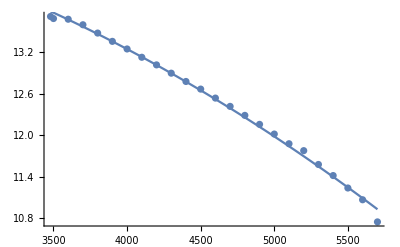

```mathematica
Show[ListPlot[data3],Plot[nlm3[x],{x,3480,5701}]]
```

```mathematica
data4 = {{0,.3403},{1.524,.3344},{3.048,0.3284},{4.572,.3222},{6.096,.3160}};
nlm4 = NonlinearModelFit[data4,a^2-b^2 x^2,{a,b},x]
```

FittedModel[0.336674-0.000603769 x^2]

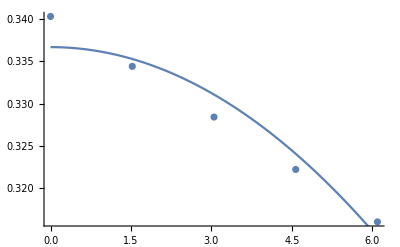

```mathematica
Show[ListPlot[data4],Plot[nlm4[x],{x,0,6.096}]]
```